```mathematica
Import["libs/QuantumDavid.m"]
```

```mathematica
Matrices=Table[Table[
MatrixPower[matrixU[LM[0,Pi/2,40][[i]]
,0,16,5],k],{i,1,40}],{k,1,12}];
```

```mathematica
x=Import["trazas.txt","Table"]//ToExpression;
```

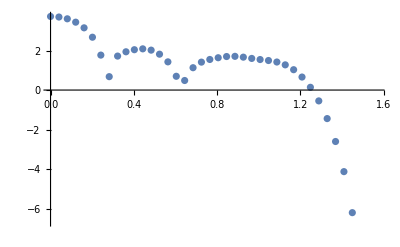

```mathematica
ListPlot[Table[{LM[0,Pi/2,40][[i]],Log[10,Abs[x[[5]][[i]]]^2]},{i,1,40}]]
```